# Решение задачи штейнера на больших графах

## Фёдор Курмазов, ПМ-2041

## Задача штейнера на графе.

#### Постановка задачи:

Steiner tree problem in graphs, далее STP:
Для данного взвешенного неориентированного графа G=(V,E) и множества терминалов T⊆V, требуется найти остовный подграф S графа G наименьшего веса, стягивающий множество T.

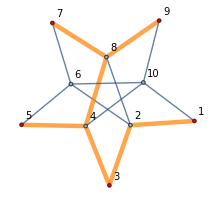

Опр. Для S - допустимого решения задачи, вершиной штейнера называется u ∈ S, u ∉ T.

#### Сложность решения :

Задача разрешимости соответствующая STP является NP-полной.

Оптимизационная версия STP является NP-сложной.

Метрическая STP является APX-полной.

## Структура проекта

#### Организация работы:

Результатом работы является пакет .wl.

Основной функционалт также распределен по пакетам.

Для контроля версий использовался Git и GitHub.

Структура проекта: -Graphics-

## Реализованные алгоритмы

#### Точные решения :

(DW) Алгоритм Дрейфуса-Вагнера. Динамическое программирование.			 O(3^t n+2^t n^2+poly())

#### Приближения :

(DNH) 2-приближение, алгоритм Коу-Марковского-Бермана. 		     				O(t m log(n))  
(DNHA) 2-приближение, алгоритм Мельхорна. 					    				O(m log(n))

#### Жадные :

(SPH) Кратчайшие путей. 													      	O(n m log(n))
(RSPH) Повторные кратчайшие пути.												O(n m log(n))

#### Локальный поиск:

(VI) Вставка вершины штейнера.
(VE) Удаление вершины штейнера.
(PE) Обмен ключевыми путями. 													O(n m log(n))

## 2-приближение

#### Алгоритм Коу-Марковского-Бермана:

Построить метрическое замыкание G^* индуцированного графа G[T].

Найти в G^* минимальное остовное дерево.

Найти соответствующие ему пути в G.

Найти минимальное остовное дерево графа из полученных путей.

Почистить граф.

#### Время работы:

На 1-ом шаге, для построение метрического замыкания графа, алгоритм вычисляет кратчайшие пути от каждого терминала t∈T до остальных терминалов.

Это занимает O(|T|m log(n)), что плохо при большом количестве терминалов.

#### Алгоритм Мельхорна:

Цель - ускорить первый шаг алгоритма до O(m log n).

Вместо пересчета расстояния от каждой вершины до каждой можно построить диаграмму Вороного.

## Диаграммы Вороного

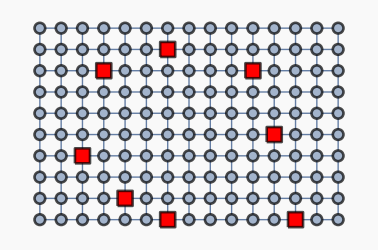
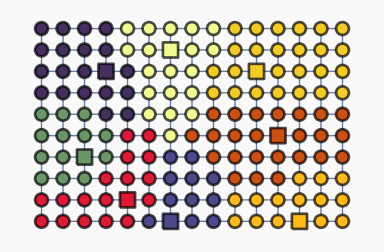
```mathematica
-Graphics-     ->     -Graphics-
```

Множество вершин V разбивается на подмножества относительно заданного множества вершин-центров C ⊆ V таким образом, что u ∈ V_k если вершина k ∈ C является близжайшим центром u.

#### Алгоритм Мельхорна:

По граничным ребрам диаграммы востанавливаются пути между терминалами.

Из данных ребер формируется граф, и в находится минимальное остовное дерево.

Это дерево соответствует дереву в G^* пореберно.

## Локальный поиск.

## Результаты работы

0. Изучена литература.
1. Генерация случайных экземпляров задачи, и визуализация.
2. Точное решение задачи алгоритмом Дрейфуса-Вагнера O*(n 3^t).
3. 2-приближенное решение задачи алгоритмом Коу-Марковски-Бермана O(|T|(m log n)), и алгоритмом Мельхорна-Коу O(m log n), с использованием построение диаграм Вороного O(m log n).
4. Алгоритмы локального поиска steiner-vertex insertion, steiner-vertes elimination, key-path exchange, с использованием продвинутых структур данных (левосторонние кучи, СНМ).
5. Код структурирован и распределен по пакетам (.wl).


Приятный дополнительный выход: мини-пакет тестирования функций, пакет со структурой данных "левосторонняя куча", реализованной в рекурсивно-функциональном стиле на вложенных списках (LinkedList).

## init